```mathematica
(* 未经作者同意请不要复制或转载本文任何内容 *)
(* @By wuwc *)
(* @EMail: brucecen2@gmail.com *)
```

```mathematica
(*计算包含单位，事实上mathematica并不知道这是单位*)
distance = 10 m;
time = 2 s;
speed = distance / time

c= 2.99*10^8 m/s;
lambda = 1.0 * 10^(-6) m;
nu = c / lambda
```

(5 m)/s

(2.99×10^14)/s

```mathematica
h = 6.626 * 10^(-34) J s;
e = h * nu
```

1.98117×10^-19 J

```mathematica
n = 1.00 mol;
r = 0.08206 (L atm) / (K mol);
t = 273 K;
v = 1.00 L;
p = n * r * t  / v
```

22.4024 atm

```mathematica
(*funny case*)
r = 8.314 J / (K mol);
t = 300 K;
m = 0.02802 kg/mol;
uaverage = ((8 * r * t)/(Pi * m))^(1/2)
```

476.104 √(J/kg)

```mathematica
(*导入mathematica单位*)
<< Units`
```

```mathematica
$Packages
```

{Units`,ResourceLocator`,DocumentationSearch`,GetFEKernelInit`,JLink`,PacletManager`,WebServices`,System`,Global`}

```mathematica
Names["Units`*"]
```

```mathematica
{"Abampere","Abcoulomb","Abfarad","Abhenry","Abmho","Abohm","Abvolt","Acre","Amp","Ampere","AMU","Angstrom","Apostilb","ArcMinute","ArcSecond","Are","AssayTon","AstronomicalUnit","Atmosphere","AtomicMassUnit","Atto","AU","AvoirdupoisOunce","AvoirdupoisPound","Bag","BakersDozen","Bale","Bar","Barn","Barrel","Barye","Baud","Becquerel","Biot","Bit","BoardFoot","BohrMagneton","Bolt","BritishThermalUnit","BTU","Bucket","Bushel","Butt","Cable","Caliber","Calorie","Candela","Candle","Carat","Celsius","Cental","Centi","Centigrade","Centimeter","Century","CGS","Chain","ChevalVapeur","Cicero","Convert","ConvertTemperature","Cord","Coulomb","Cubit","Curie","Dalton","Day","Deca","Decade","Deci","Denier","Didot","DidotPoint","Diopter","Dozen","Drachma","Dyne","ElectronVolt","Ell","Ephah","Erg","Exa","Fahrenheit","Farad","Fathom","Feet","Femto","Fermi","Fifth","Firkin","FluidDram","FluidOunce","Foot","FootCandle","Fortnight","Furlong","Gal","Gallon","Gauss","Geepound","Giga","Gilbert","Gill","Grade","Grain","Gram","GramWeight","Gravity","GrayDose","Gross","GrossHundredweight","Hand","Hectare","Hecto","Hefner","Henry","Hertz","Hogshead","Horsepower","Hour","Hundredweight","ImperialGallon","ImperialPint","Inch","InchMercury","Jeroboam","Jigger","Joule","Kayser","Kelvin","Kilo","Kilogram","KilogramForce","KilogramWeight","Knot","Lambert","League","Libra","LightYear","Link","Liter","LongTon","Lumen","Lumerg","Lux","Magnum","Maxwell","Mega","Meter","MetricTon","Mho","Micro","Micron","Mil","Mile","Millennium","Milli","MillimeterMercury","Mina","Minim","Minute","MKS","Mole","Month","Nano","NauticalMile","NetHundredweight","Newton","Nibble","Nit","Noggin","NuclearMagneton","Obolos","Oersted","Ohm","Omer","Ounce","Parsec","Pascal","Peck","Pennyweight","Percent","Perch","Peta","Phot","Pica","Pico","Pint","Poise","Pole","Pondus","Pony","Pound","Poundal","PoundForce","PoundsPerSquareInch","PoundWeight","PrintersPoint","PSI","Puncheon","Quadrant","Quart","Quintal","Rad","Radian","Rankine","RegisterTon","Reyn","Rhes","RightAngle","Rod","Roentgen","Rontgen","Rood","Rope","Rutherford","Rydberg","Seam","Second","Section","Shekel","ShortHundredweight","ShortTon","Shot","SI","SiderealSecond","SiderealYear","Siemens","Skein","Slug","SolarMass","Stadion","Stadium","Statampere","Statcoulomb","Statfarad","Stathenry","Statohm","StatuteMile","Statvolt","Steradian","Stere","Stilb","Stokes","Stone","SurveyMile","Tablespoon","Talbot","Talent","Teaspoon","Tera","Tesla","Therm","Ton","TonForce","Tonne","Torr","Township","TropicalYear","TroyOunce","Tun","UKGallon","UKPint","Volt","Watt","Weber","Week","Wey","WineBottle","XUnit","Yard","Year","Yocto","Yotta","Zepto","Zetta"}
```

```mathematica
?Butt
```

Butt is a unit of volume.

```mathematica
?Newton
```

Newton is the derived SI unit of force.

```mathematica
Convert[1 Atmosphere, Pascal]
```

101325. Pascal

```mathematica
?Tesla
```

Tesla is the derived SI unit of magnetic flux density.

```mathematica
Convert[10 Kilo Meter, Mile]
```

(78125 Mile)/12573

```mathematica
N[%]
```

6.21371 Mile

```mathematica
Convert [474 Meter/Second, Mile/Hour]
```

(1481250 Mile)/(1397 Hour)

```mathematica
N[%]
```

(1060.31 Mile)/Hour

```mathematica
ConvertTemperature[72, Fahrenheit, Celsius]
```

200/9

```mathematica
N[%]
```

22.2222

```mathematica
ConvertTemperature[0, Celsius, Kelvin]
```

5463/20

```mathematica
N[%]
```

273.15

```mathematica
<<PhysicalConstants`
```

```mathematica
$Packages
```

{PhysicalConstants`,Units`,ResourceLocator`,DocumentationSearch`,GetFEKernelInit`,JLink`,PacletManager`,WebServices`,System`,Global`}

```mathematica
Names["PhysicalConstants`*"]
```

{AccelerationDueToGravity,AgeOfUniverse,AvogadroConstant,BohrRadius,BoltzmannConstant,ClassicalElectronRadius,CosmicBackgroundTemperature,DeuteronMagneticMoment,DeuteronMass,EarthMass,EarthRadius,ElectronCharge,ElectronComptonWavelength,ElectronGFactor,ElectronMagneticMoment,ElectronMass,FaradayConstant,FineStructureConstant,GalacticUnit,GravitationalConstant,HubbleConstant,IcePoint,MagneticFluxQuantum,MolarGasConstant,MolarVolume,MuonGFactor,MuonMagneticMoment,MuonMass,NeutronComptonWavelength,NeutronMagneticMoment,NeutronMass,PlanckConstant,PlanckConstantReduced,PlanckMass,ProtonComptonWavelength,ProtonMagneticMoment,ProtonMass,QuantizedHallConductance,RydbergConstant,SackurTetrodeConstant,SolarConstant,SolarLuminosity,SolarRadius,SolarSchwarzschildRadius,SpeedOfLight,SpeedOfSound,StefanConstant,ThomsonCrossSection,VacuumPermeability,VacuumPermittivity,WeakMixingAngle}

```mathematica
AvogadroConstant
```

(6.02214×10^23)/Mole

```mathematica
MolarGasConstant
```

(8.31447 Joule)/(Kelvin Mole)

```mathematica
FaradayConstant
```

(96485.3 Coulomb)/Mole

```mathematica
SpeedOfLight
```

(299792458 Meter)/Second

```mathematica
lambda = 1.0 * 10^-6 Meter;
nu = SpeedOfLight/lambda
```

(2.99792×10^14)/Second

```mathematica
e = PlanckConstant * nu
```

1.98645×10^-19 Joule

```mathematica
√π
```

√π

```mathematica
N[%]
```

1.77245

```mathematica
√2
```

√2

```mathematica
N[%]
```

1.41421

```mathematica
27^(1/3)
```

3

```mathematica
θ = 2 * π;
Cos[θ]
```

1

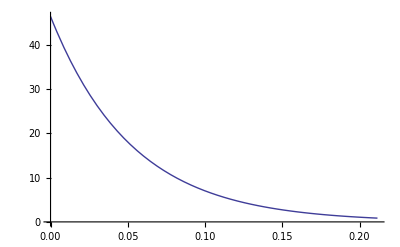

```mathematica
(*Functions*)
ψ[r_] := (1/(π Subscript[a, 0]^3))^(1/2)ⅇ^(-r/Subscript[a, 0]);
Subscript[a, 0] = 0.0529;(*Bohr radius in nm*)
Plot[ψ[r], {r, 0, 4*Subscript[a, 0]}]
```

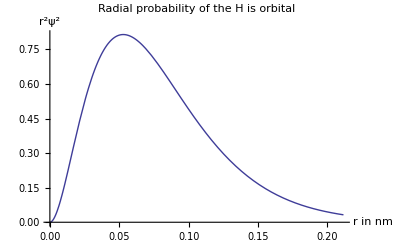

```mathematica
Plot[r^2(ψ[r])^2, {r, 0, 4*Subscript[a, 0]},
AxesLabel->{"r in nm", "r^2ψ^2"},
PlotLabel->"Radial probability of the H is orbital"]
```

```mathematica
(*replacement rule*)
Clear[e, nu, h]
```

```mathematica
e = h * nu
```

h nu

```mathematica
h = 6.626 * 10^-34;
e
```

6.626×10^-34 nu

```mathematica
nu = 3*10^14;
e
```

1.9878×10^-19

```mathematica
Clear[e, nu];
```

```mathematica
e = h nu
```

6.626×10^-34 nu

```mathematica
e/.nu->3*10^14
```

1.9878×10^-19

```mathematica
e
```

6.626×10^-34 nu

```mathematica
Clear[p, v, t];
```

```mathematica
<< PlotLegends`
```

```mathematica
$Packages
```

{PlotLegends`,ResourceLocator`,DocumentationSearch`,GetFEKernelInit`,JLink`,PacletManager`,WebServices`,System`,Global`}

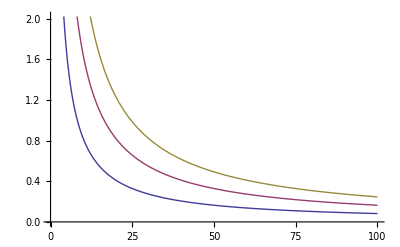

```mathematica
r = 0.08206;
n=1;
p[v_]:=n*r*t/v;
Plot[{p[v]/.t->100,p[v]/.t->200,p[v]/.t->300}, {v, 0, 100},
PlotLegend->{"T=100K", "T=200K", "T=300K"}]
```

```mathematica
(*List and Table*)
```

```mathematica
Clear[c,e];
letters={a,b,c,d,e}
```

{a,b,c,d,e}

```mathematica
integers={1,2,3}
```

{1,2,3}

```mathematica
reals={10.0,44.7,61.3,76.5,88.1}
```

{10.,44.7,61.3,76.5,88.1}

```mathematica
(*Automatically create lists*)
squares=Table[i^2,{i,1,100}](*1 for default increment*)
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400,441,484,529,576,625,676,729,784,841,900,961,1024,1089,1156,1225,1296,1369,1444,1521,1600,1681,1764,1849,1936,2025,2116,2209,2304,2401,2500,2601,2704,2809,2916,3025,3136,3249,3364,3481,3600,3721,3844,3969,4096,4225,4356,4489,4624,4761,4900,5041,5184,5329,5476,5625,5776,5929,6084,6241,6400,6561,6724,6889,7056,7225,7396,7569,7744,7921,8100,8281,8464,8649,8836,9025,9216,9409,9604,9801,10000}

```mathematica
squares=Table[i^2,{i,10,1,-1}]
```

{100,81,64,49,36,25,16,9,4,1}

```mathematica
recip=Table[1/i,{i,1,9,2}]
```

{1,1/3,1/5,1/7,1/9}

```mathematica
f[x_]:=1/x^2;
Table[f[x],{x,1,10}]
```

{1,1/4,1/9,1/16,1/25,1/36,1/49,1/64,1/81,1/100}

```mathematica
(*Query elements*)
Length[letters]
```

5

```mathematica
Length[squares]
```

10

```mathematica
First[letters]
```

a

```mathematica
Last[letters]
```

e

```mathematica
letters[[2]]
```

b

```mathematica
letters[[3]]
```

c

```mathematica
(*Make a new list by using old list*)
letters2=Take[letters,3]
```

{a,b,c}

```mathematica
Take[letters,-3]
```

{c,d,e}

```mathematica
Reverse[letters]
```

{e,d,c,b,a}